{{u→Function[{t},-1/(7 (-1+√7 π-2 π^2) (1+√7 π+2 π^2))ⅇ^(-t/2) (14 π Cos[(√7 t)/2]-√7 ⅇ^(t/2) Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]-7 ⅇ^(t/2) π Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]-2 √7 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]+√7 ⅇ^(t/2) Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]-7 ⅇ^(t/2) π Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]+2 √7 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]-6 √7 π Sin[(√7 t)/2]+16 √7 π^3 Sin[(√7 t)/2]+7 ⅇ^(t/2) Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]+3 √7 ⅇ^(t/2) π Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-14 ⅇ^(t/2) π^2 Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-8 √7 ⅇ^(t/2) π^3 Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-7 ⅇ^(t/2) Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]+3 √7 ⅇ^(t/2) π Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]+14 ⅇ^(t/2) π^2 Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]-8 √7 ⅇ^(t/2) π^3 Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]-7 ⅇ^(t/2) Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]-3 √7 ⅇ^(t/2) π Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]+14 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]+8 √7 ⅇ^(t/2) π^3 Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]-√7 ⅇ^(t/2) Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]-7 ⅇ^(t/2) π Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]-2 √7 ⅇ^(t/2) π^2 Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]+7 ⅇ^(t/2) Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]-3 √7 ⅇ^(t/2) π Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]-14 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]+8 √7 ⅇ^(t/2) π^3 Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]+√7 ⅇ^(t/2) Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t]-7 ⅇ^(t/2) π Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t]+2 √7 ⅇ^(t/2) π^2 Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t])]}}

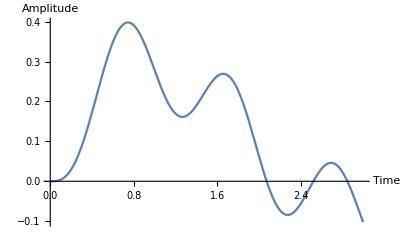

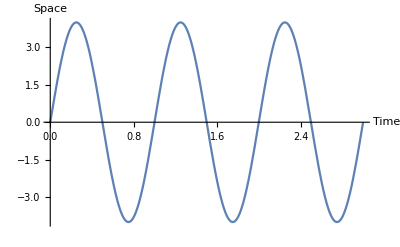

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\forced_oscillator\data.csv

```mathematica
L=1;
f[t_]:= Sin[2*Pi*t]*4;
m=1;
gamma=1;
k=2;
tm = 3;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=DSolve[{eqn,initialConditions},u,t]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bacPI_GP_regressor\\data_files\\data.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```